```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Import["../General.m"];
```

```mathematica
temperatureData=Import["/home/nathan/olin/fall2016/qEAFall2016Homework/bset4/BostonTempData.mat","Data"];
```

```mathematica
Dimensions@temperatureData
```

{3,8760,1}

```mathematica
dni=Flatten[temperatureData[[1]]];
hour=Flatten[temperatureData[[2]]];
temp=Flatten[temperatureData[[3]]];
```

### Plot of temperature vs hours for the entire year. Highest temp is 36c or 96f. Lowest temp is -20c or -4f.

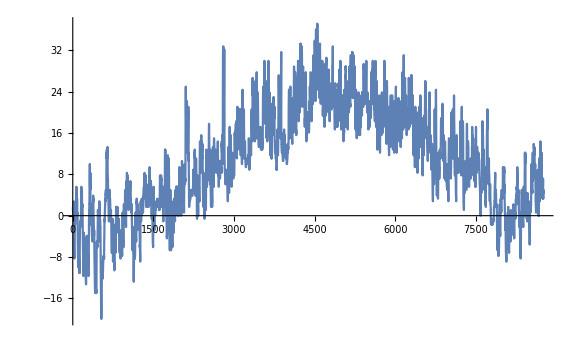

```mathematica
ListLinePlot[temp,ImageSize->Large]
```

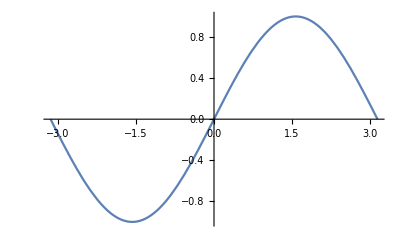

```mathematica
Plot[Sin[θ],{θ,-Pi,Pi}]
```

### Plot of dni over the course of a year. You can see that some parts are more dense than others. I think this shows that some days in the summer get more sunlight than those in the winter.

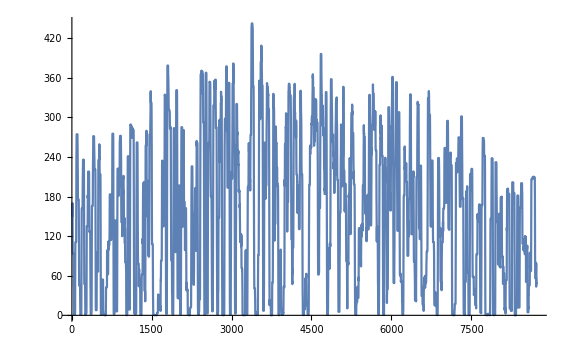
```mathematica
ListLinePlot[dni,ImageSize->Large]-Graphics-
```

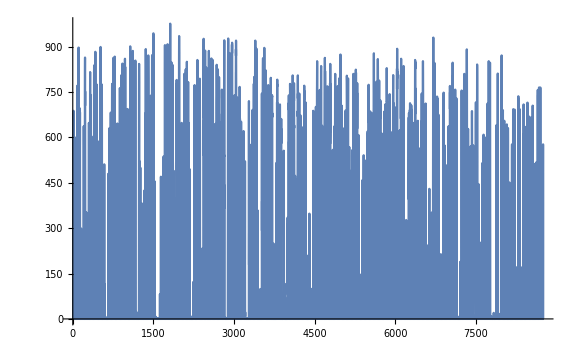
-Graphics- -Graphics-

### Moving average half a year long cyclic convolutions. Here we can see the lowest frequency. This is how the sun behaves over the course of year.

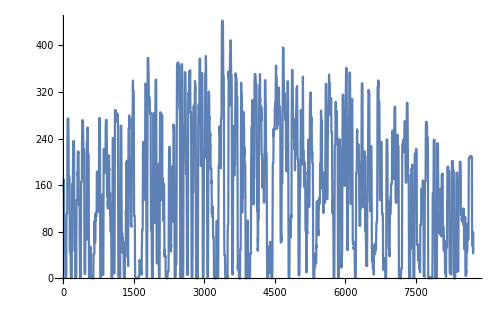

```mathematica
ListLinePlot[ListConvolve[ConstantArray[1/24,24],dni]]
```

### Moving averages over the course a month

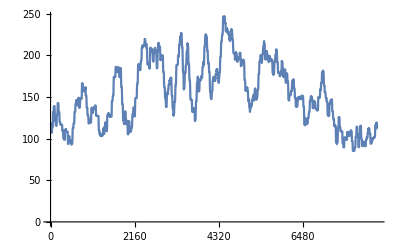

```mathematica
ListLinePlot[ListConvolve[ConstantArray[1/360,360],dni],Ticks->{Range[0,8760,24*30],Range[0,250,50]}]
```

### Plot of dni for 5 random days. I’m interested why hours 35 to 70 have zero sunlight. Maybe there was a full day solar eclipse.

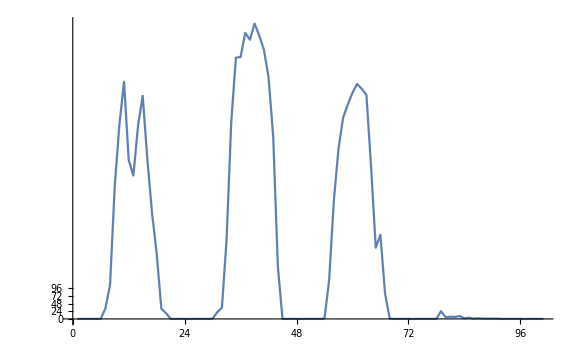

```mathematica
ListLinePlot[dni[[3000;;3100]],ImageSize->Large,PlotRange->Full,Ticks->{Range[0,100,24]}]
```

### Two random days during the year. The plot starts during the night and it gets colder. During daytime, the temperature increases.

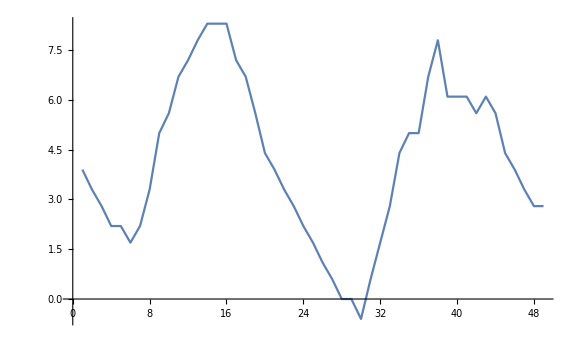

```mathematica
ListLinePlot[temp[[2424;;2472]],ImageSize->Large]
```

### Plot of dmi vs hour for the two random days. We can see daylight hours give us sunlight which increases temperature.

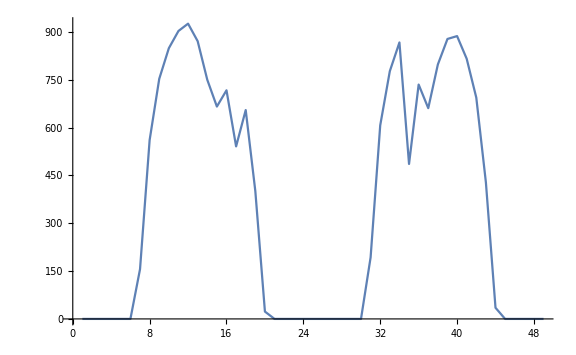

```mathematica
ListLinePlot[dni[[2424;;2472]],ImageSize->Large]
```

### A zoomed in view of the temperature fft. The huge peak at the low frequency (peaks at 1000), represents the overall trend for the year. The peak at index 365ish represents the temperatures over a 24 hour period.

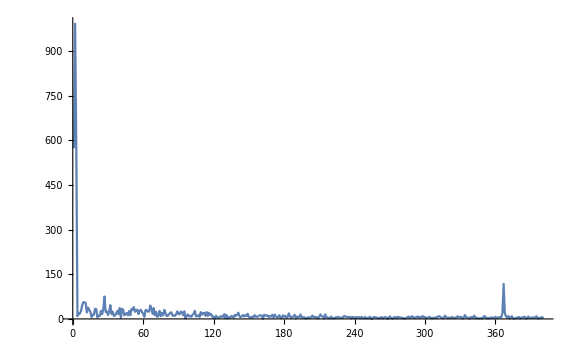

```mathematica
ListLinePlot[Abs[fftShift[temp][[Round@(Length[temp]/2);;Round@(Length[temp]/2)+400]]],ImageSize->Large,PlotRange->All]
```

```mathematica
24*365
```

8760

```mathematica
plot
```

plot

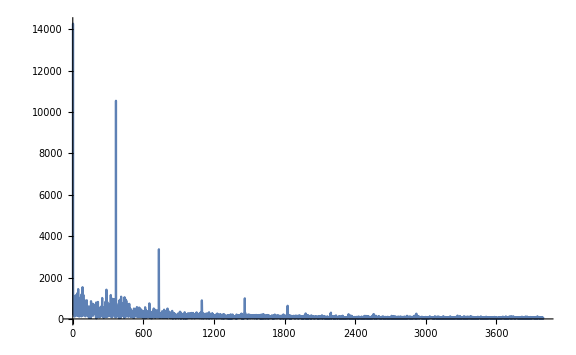

```mathematica
ListLinePlot[Abs[fftShift[dni][[Round@(Length[temp]/2);;Round@(Length[temp]/2)+4000]]],ImageSize->Large,PlotRange->All]
```

## 3b - doing pre-work calculations

```mathematica
r[t_]:=A*Cos[2Pi*v*t]/L
```

```mathematica
r[t]
```

(A Cos[2 π t v])/L

```mathematica
D[(A Cos[2 π t v])/L, t]
```

-(2 A π v Sin[2 π t v])/L

```mathematica
exportNotebookPDF[]
```

/home/nathan/olin/fall2016/qEAFall2016Homework/bset4/bset4Scrapbook.pdf